We simulate reversible bitfuck (RBF)!

We use a list of characters to represent the program code, and Tape[x___] for the tape.

At each position in the Tape, we can have either a boolean integer (0 or 1) or the tape head, which is represented as LeftTriangle[b_, program_] (i.e. b_ ⊲ program_). Ideally this would instead be WithHead, and we’d just have notation and formatting that made it synonymous with LeftTriangle.

The program consists of a list of characters, one of which is wrapped in At, which specifies which character the program head is at.

Aside: it’s interesting to me how we essentially have two tapes and two tape heads: one for the actual data, and one for the code. I guess we could simulate this with more hardcoded rules and a longer tape, and then we wouldn’t need both. But what about the other direction? A program that specifies how to read the program?

### Datatypes & computation

The language for RBF.

```mathematica
L={"*","<",">","(",")"};
l=Alternatives@@L;
```

Jump forward or backward through code adjacent to a parenthesis until we reach a matching parenthesis. (Note that p is assumed to not include the parenthesis we’re matching.

```mathematica
JumpForward[p:l...]:=Sequence@@Catch[
{{},{p},1}//.{
{{p0:l...},{c:l,p1:l...},n_?Positive}:>{{p0,c},{p1},n+Switch[c,"(",1,")",-1,_,0]},
{{p0:l...},{},_}:>Throw[{p0,At[End]}],
{{p0:l...},{c:l,p1:l...},0}:>Throw[{p0,At[c],p1}]
}
]
```

```mathematica
JumpBackward[p:l...]:=Sequence@@Catch[
{{p},{},1}//.{
{{p0:l...,c:l},{p1:l...},n_?Positive}:>{{p0},{c,p1},n+Switch[c,"(",-1,")",1,_,0]},
{{p0:l...},{bracket:l,c:l,p1:l...},0}:>Throw[{p0,bracket,At[c],p1}],
{{},{p1:l...},_}:>Throw[{At[End],p1}]
}
]
```

```mathematica
ToggleBit[0]=1;ToggleBit[1]=0;
```

Move At to the next character. If there isn’t one, insert End.

```mathematica
AtNext[c_,p___]:=Sequence[At[c],p]
AtNext[]:=At[End]
```

Put the program head at the next or previous tape value (bit). Assumes a rightward-infinite tape but not a leftward-infinite one. (If we were being more general this would be changeable.)

```mathematica
NextBit/:NextBit[b:(0|1),bs:(0|1)...]⊲program_List:=Sequence[b⊲program,bs]
NextBit/:NextBit[]⊲program_List:=0⊲program
```

```mathematica
PrevBit/:PrevBit[bs:(0|1)...,b:(0|1)]⊲program_List:=Sequence[bs,b⊲program]
PrevBit/:PrevBit[]⊲program_List:=TapeEnd
```

The rules for RBF. Note that if we breach the left end of the tape, we get an InertTape. If the program attempts to read characters which are out of bounds and thus halts, we get a FinalTape.

```mathematica
RBF={
Tape[b0:(0|1)...,0⊲{p0:l...,At["("],p1:l...},b1:(0|1)... ]:>
Tape[b0,0⊲{p0,"(",JumpForward[p1]},b1],
Tape[b0:(0|1)...,0⊲{p0:l...,At[")"],p1:l...},b1:(0|1)... ]:>Tape[b0,0⊲{JumpBackward[p0],")",p1},b1],
Tape[b0:(0|1)...,1⊲{p0:l...,At[p:"("|")"],p1:l...},b1:(0|1)... ]:>
Tape[b0,1⊲{p0,p,AtNext[p1]},b1],
Tape[b0:(0|1)...,(b:(0|1))⊲{p0:l...,At["*"],p1:l...},b1:(0|1)... ]:>
Tape[b0,ToggleBit[b]⊲{p0,"*",AtNext[p1]},b1],Tape[b0:(0|1)...,(b:(0|1))⊲{p0:l...,At[">"],p1:l...},b1:(0|1)... ]:>
Tape[b0,b,NextBit[b1]⊲{p0,">",AtNext[p1]}],Tape[b0:(0|1)...,(b:(0|1))⊲{p0:l...,At["<"],p1:l...},b1:(0|1)... ]:>
Tape[PrevBit[b0]⊲{p0,"<",AtNext[p1]},b,b1],
Tape[TapeEnd,b:(0|1)...]:>InertTape[b],
Tape[b0:(0|1)...,(b:(0|1))⊲(p:({___,At[End]}|{At[End],___})),b1:(0|1)...]:>FinalTape[b0,TapeAt[b],b1]
};
```

Run an RBF program on an initial tape of 0’s.

```mathematica
RunRBF[{p:l...}]:=ReplaceRepeated[Tape[0⊲{AtNext[p]}],RBF,MaxIterations->$MaxSteps]
RunRBF[p_String]:=RunRBF[Characters[p]]
```

A global variable putting a cap on how long traces can be. Could be better implemented as an option.

```mathematica
$MaxSteps=40;
```

```mathematica
TraceRBF[{p:l...}]:=RBFTracedEvaluation@@Most@FixedPointList[Replace[RBF],Tape[0⊲{AtNext[p]}],$MaxSteps]
TraceRBF[p_String,args___]:=TraceRBF[Characters[p],args]
```

Run a program on a pure data tape given an index specifying the initial head location (which is 1 if unspecified)

```mathematica
TraceRBF[p:{l...},t: Tape[(0|1)..],n_Integer?Positive:1]/;n<=Length[t]:=RBFTracedEvaluation@@Most@FixedPointList[Replace[RBF],MapAt[#⊲p&,Tape@@t,n],$MaxSteps]
```

Given a Tape with a TapeAt location, run p with head starting there

```mathematica
TraceRBF[{p:l...},Tape[x___,TapeAt[b_],y___]]:=RBFTracedEvaluation@@Most@FixedPointList[Replace[RBF],Tape[x,b⊲{AtNext[p]}],$MaxSteps]
```

Compute the inverse of an RBF program.

```mathematica
RBFReverse[p_String]:=StringReverse@StringReplace[p,{")"->"(","("->")",">"->"<","<"->">"}]
```

Attempt a random picofuck translation.

```mathematica
PFtoRBF={"["->"*(*>(","]"->"*<)"};
```

To really explore picofuck, what we need to do is study the “automorphisms” of RBF. A simple translation is...sort of an adjunction between two languages. By trying to construct

### Formatting

Ways to format things. We use a global variable $StyleSelection so that we can support multiple styles through Format.

Note that using options for this is a bit tricky, since we want to 1) return the bare data, not formatting primitives like Grid and 2) keep the actual data optionless (e.g., At should not take options). One solution might be to put options in e.g. RBFTracedEvaluation only, and only attach format rules to that. But I'd prefer having the format values attached to the primitives themselves.

You can specify $StyleSelection to be a function which acts on the primitives in question.

```mathematica
$StyleSelection=Automatic;
StyleSelector[x_,s:Except[Automatic|_String]]:=s[x]
```

```mathematica
Format[At[x_]]:=StyleSelector[At[x],$StyleSelection]
```

```mathematica
StyleSelector[At[End],Automatic]:=Highlighted[" ",ContentPadding->False,Background->Green]
StyleSelector[(At|TapeAt)[x_],Automatic]:=
Highlighted[Style[x,Bold],ContentPadding->False,FrameMargins->{{None,None},{Automatic,Automatic}}]
```

```mathematica
StyleSelector[At[End],"Delicate"]:=Highlighted[◼,ContentPadding->False,Frame->True,FrameMargins->Small,FrameStyle->Green,Background->None]
StyleSelector[(At|TapeAt)[x_],"Delicate"]:=
Highlighted[Style[x,Bold],ContentPadding->False,FrameMargins->{{None,None},{Automatic,Automatic}},Frame->True,Background->None]
```

```mathematica
Format[b_⊲{p___}]:=b⊲Row[{p}]
```

```mathematica
Format[Tape[a___,b_TapeAt,c___]]:=StyleSelector[Tape[a,b,c],$StyleSelection]
```

```mathematica
StyleSelector[Tape[a___,b_TapeAt,c___],Automatic]:=Grid[{{a,Item[b,Background->Opacity[0.6,Cyan]],c,""}},Dividers->All,Background->{{{None},Black},{}}]
StyleSelector[Tape[a___,b_TapeAt,c___],"Delicate"]:=Grid[{{a,Item[b,Frame->True,FrameStyle->Cyan],c}}]
```

```mathematica
Format[TapeAt[x_]]:=x
```

```mathematica
Format[Tape[a___]]:=Grid[{{a,""}},Dividers->All,Background->{{{None},Black},None}]
```

```mathematica
Format[InertTape[a___]]:=Grid[{{a}},Dividers->All,Background->LightRed]
```

```mathematica
Format[FinalTape[a___]]:=StyleSelector[FinalTape[a],$StyleSelection]
```

```mathematica
StyleSelector[FinalTape[a___],Automatic]:=Grid[{{a}}/.{TapeAt[x_]:>x,LeftTriangle[x_,_]:>x},Dividers->All,Background->LightGreen]
StyleSelector[FinalTape[a___],"Delicate"]:=Grid[{{a}}/.{TapeAt[x_]:>x,LeftTriangle[x_,_]:>x},Dividers->All,FrameStyle->Green]
```

```mathematica
Format[RBFTracedEvaluation[a___Tape,b:_Tape|_FinalTape|_InertTape]]:=Column[{a,b}]
```

Moves the program outside the Tape, relying on TapeAt instead. Useful for visualization.

```mathematica
SeparateCode[Tape[x___,LeftTriangle[b_,code_],y___]]:=WithCode[Tape[x,TapeAt[b],y],code]
SeparateCode[t:_Tape|_FinalTape|_InertTape]:=WithCode[t,{}]
SeparateCode[x_RBFTracedEvaluation]:=SeparateCode/@x
```

```mathematica
IntegrateCode[WithCode[(t:(Tape|InertTape|FinalTape))[x___,TapeAt[b_],y_],code_]]:=t[x,b⊲t,y]
```

```mathematica
Format[RBFTracedEvaluation[x__WithCode]]:=Grid[{x}/.WithCode[t_,c_]:>{t,Row[c]},Alignment->Left]
```

## Visualizations

```mathematica
TraceRBF["*(>()*)"]
```

0⊲*(>()*) | 
1⊲*(>()*) | 
1⊲*(>()*) | 
1 | 0⊲*(>()*) | 
1 | 0⊲*(>()*) | 
1 | 1⊲*(>()*) | 
1 | 1⊲*(>()*)  | 
1 | 1

Apply the inverse of a bitfuck program. Note that we wind up with an all-0 tape.

Evaluation is shown top-to-bottom for the original program and bottom-to-top for the reversed one.

Note that when running the inverse program, we start with the head at its final position from the original program's evaluation.

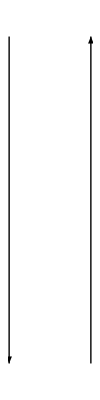
0 |  | >*(*)(>*>*)
0 | 0 |  | >*(*)(>*>*)
0 | 1 |  | >*(*)(>*>*)
0 | 1 |  | >*(*)(>*>*)
0 | 0 |  | >*(*)(>*>*)
0 | 0 |  | >*(*)(>*>*)
0 | 1 |  | >*(*)(>*>*)
0 | 1 |  | >*(*)(>*>*)
0 | 1 |  | >*(*)(>*>*)
0 | 1 | 0 |  | >*(*)(>*>*)
0 | 1 | 1 |  | >*(*)(>*>*)
0 | 1 | 1 | 0 |  | >*(*)(>*>*)
0 | 1 | 1 | 1 |  | >*(*)(>*>*)
0 | 1 | 1 | 1 |  | >*(*)(>*>*) -Graphics-0 | 0 | 0 | 0 |  | (*<*<)(*)*< 
0 | 0 | 0 | 0 |  | (*<*<)(*)*<
0 | 1 | 0 | 0 |  | (*<*<)(*)*<
0 | 1 | 0 | 0 |  | (*<*<)(*)*<
0 | 0 | 0 | 0 |  | (*<*<)(*)*<
0 | 0 | 0 | 0 |  | (*<*<)(*)*<
0 | 1 | 0 | 0 |  | (*<*<)(*)*<
0 | 1 | 0 | 0 |  | (*<*<)(*)*<
0 | 1 | 0 | 0 |  | (*<*<)(*)*<
0 | 1 | 0 | 0 |  | (*<*<)(*)*<
0 | 1 | 1 | 0 |  | (*<*<)(*)*<
0 | 1 | 1 | 0 |  | (*<*<)(*)*<
0 | 1 | 1 | 1 |  | (*<*<)(*)*<
0 | 1 | 1 | 1 |  | (*<*<)(*)*<

```mathematica
With[{p=">*(*)(>*>*)"},
Row[{
Drop[TraceRBF[p],-1]//SeparateCode,
Spacer[10],Graphics[{Arrowheads[0.7],Arrow[{{0.25,-1},{0.25,1}}],Arrow[{{-0.25,1},{-0.25,-1}}]}],Spacer[10],
Reverse@Drop[TraceRBF[RBFReverse[p],Tape@@Last@TraceRBF[p]],-1]//SeparateCode}]]
```

```mathematica
$StyleSelection="Delicate";
With[{p=">*(*)(>*>*)"},
Row[{Drop[TraceRBF[p],-1]//SeparateCode,Spacer[10],Graphics[{Arrowheads[0.7],Arrow[{{0.25,-1},{0.25,1}}],Arrow[{{-0.25,1},{-0.25,-1}}]}],Spacer[10],
Reverse@Drop[TraceRBF[RBFReverse[p],Tape@@Last@TraceRBF[p]],-1]//SeparateCode}]]
```

0 | >*(*)(>*>*)
0 | 0 | >*(*)(>*>*)
0 | 1 | >*(*)(>*>*)
0 | 1 | >*(*)(>*>*)
0 | 0 | >*(*)(>*>*)
0 | 0 | >*(*)(>*>*)
0 | 1 | >*(*)(>*>*)
0 | 1 | >*(*)(>*>*)
0 | 1 | >*(*)(>*>*)
0 | 1 | 0 | >*(*)(>*>*)
0 | 1 | 1 | >*(*)(>*>*)
0 | 1 | 1 | 0 | >*(*)(>*>*)
0 | 1 | 1 | 1 | >*(*)(>*>*)
0 | 1 | 1 | 1 | >*(*)(>*>*)◼-Graphics-0 | 0 | 0 | 0 | (*<*<)(*)*<◼
0 | 0 | 0 | 0 | (*<*<)(*)*<
0 | 1 | 0 | 0 | (*<*<)(*)*<
0 | 1 | 0 | 0 | (*<*<)(*)*<
0 | 0 | 0 | 0 | (*<*<)(*)*<
0 | 0 | 0 | 0 | (*<*<)(*)*<
0 | 1 | 0 | 0 | (*<*<)(*)*<
0 | 1 | 0 | 0 | (*<*<)(*)*<
0 | 1 | 0 | 0 | (*<*<)(*)*<
0 | 1 | 0 | 0 | (*<*<)(*)*<
0 | 1 | 1 | 0 | (*<*<)(*)*<
0 | 1 | 1 | 0 | (*<*<)(*)*<
0 | 1 | 1 | 1 | (*<*<)(*)*<
0 | 1 | 1 | 1 | (*<*<)(*)*<

```mathematica
$StyleSelection=Automatic;
```

An example of a “simple automorphism” of the language. Replacing the given substrings does not change the program’s eventual behavior; compare with the above.

```mathematica
TraceRBF@StringReplace[">*(*)(>*>*)",{"("->"((",")"->")*)"}]//SeparateCode
```

0 |  | >*((*)*)((>*>*)*)
0 | 0 |  | >*((*)*)((>*>*)*)
0 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 |  | >*((*)*)((>*>*)*)
0 | 0 |  | >*((*)*)((>*>*)*)
0 | 0 |  | >*((*)*)((>*>*)*)
0 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 |  | >*((*)*)((>*>*)*)
0 | 0 |  | >*((*)*)((>*>*)*)
0 | 0 |  | >*((*)*)((>*>*)*)
0 | 0 |  | >*((*)*)((>*>*)*)
0 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 | 0 |  | >*((*)*)((>*>*)*)
0 | 1 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 | 1 | 0 |  | >*((*)*)((>*>*)*)
0 | 1 | 1 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 | 1 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 | 1 | 0 |  | >*((*)*)((>*>*)*)
0 | 1 | 1 | 0 |  | >*((*)*)((>*>*)*)
0 | 1 | 1 | 0 |  | >*((*)*)((>*>*)*)
0 | 1 | 1 | 1 |  | >*((*)*)((>*>*)*)
0 | 1 | 1 | 1 |  | >*((*)*)((>*>*)*) 
0 | 1 | 1 | 1 |

```mathematica
TraceRBF[StringReplace[">(*)>*(*)(>*(*>*<(*)",{"("->"(((",")"->")*)*)"}]]//SeparateCode
```

0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 | 0 | 0 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*)
0 | 0 | 1 | 0 | 1 |  | >(((*)*)*)>*(((*)*)*)(((>*(((*>*<(((*)*)*) 
0 | 0 | 1 | 0 | 1 |

```mathematica
TraceRBF@StringReplace[">*(*)(>*>*)",{"("->"(((",")"->")*)"}]//SeparateCode
```

0 |  | >*(((*)*)(((>*>*)*)
0 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 1 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 | 1 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 1 | 1 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 | 1 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 | 1 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 1 | 1 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 1 | 1 | 0 |  | >*(((*)*)(((>*>*)*)
0 | 1 | 1 | 1 |  | >*(((*)*)(((>*>*)*)
0 | 1 | 1 | 1 |  | >*(((*)*)(((>*>*)*) 
0 | 1 | 1 | 1 |

An example of a looping program.

```mathematica
Block[{$MaxSteps=100},TraceRBF["*((*)>*>*>**)"]]
```

0⊲*((*)>*>*>**) | 
1⊲*((*)>*>*>**) | 
1⊲*((*)>*>*>**) | 
1⊲*((*)>*>*>**) | 
0⊲*((*)>*>*>**) | 
0⊲*((*)>*>*>**) | 
1⊲*((*)>*>*>**) | 
1⊲*((*)>*>*>**) | 
1 | 0⊲*((*)>*>*>**) | 
1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 1⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0⊲*((*)>*>*>**) | 
1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1⊲*((*)>*>*>**) |

```mathematica
TraceRBF[StringReplace["[[]]][]][[[]][]]]][]]]]",PFtoRBF]]//SeparateCode
```

0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
1 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
1 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 1 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 1 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 | 1 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 | 1 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 | 1 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 1 | 1 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 1 | 1 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 1 | 1 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 1 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 1 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 1 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
1 | 0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
1 | 0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
1 | 0 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
1 | 1 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
1 | 1 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
1 | 1 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 1 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<)
0 | 1 | 0 |  | *(*>(*(*>(*<)*<)*<)*(*>(*<)*<)*(*>(*(*>(*(*>(*<)*<)*(*>(*<)*<)*<)*<)*(*>(*<)*<)*<)*<) 
0 | 1 | 0 |